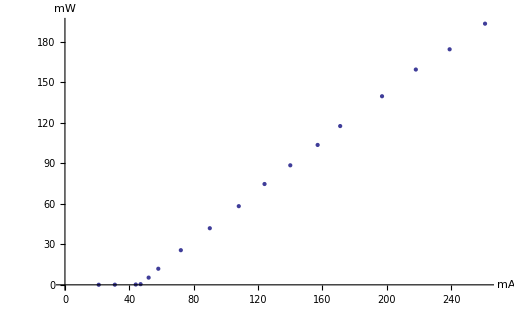

```mathematica
mA={21,31,44,47,52,58,72,90,108,124,140,157,171,197,218,239,261};
mW=Join[{66.7,118.2,237,497}/10^3,{5.35,11.93,25.68,41.96,58.31,74.74,88.6,103.7,117.7,139.8,159.6,174.6,193.6}];
PI=Thread[{mA,mW}];
ListPlot[PI,AxesLabel->{"mA","mW"}]
```

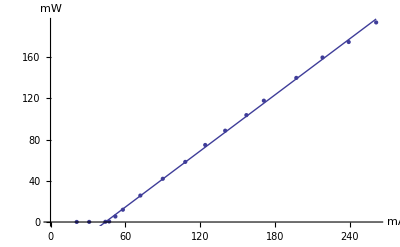

```mathematica
fitfn=a x + b;
fit=FindFit[PI[[4;;]],fitfn, {a,b},x];
Show[{ListPlot[PI,AxesLabel->{"mA","mW"}],
Plot[fitfn/.fit,{x,0,mA[[-1]]}]}]
```

```mathematica
x/.Solve[fitfn==0,x][[1,1]]/.fit
"threshold = "<>ToString[%]<>" mA"

a/.fit
"η = "<>ToString[%]<>" mW/mA"
```

44.0222

threshold = 44.0222 mA

0.9077

η = 0.9077 mW/mA